```mathematica
SetDirectory["/media/vanniagm/36887AD4887A925B/nu_portal/MATH_NUMODEL/"]
```

/media/vanniagm/36887AD4887A925B/nu_portal/MATH_NUMODEL

```mathematica
ParentDirectory[]
```

/media/vanniagm/36887AD4887A925B/nu_portal

Mapping from true coordinates {u,v} (published graph) to local coordinates (coordinates in the screen) {x,y}

Transformation:  y_i=A_y log(v_i) + B_y       x_i= A_x log(u_i) + B_x     // To find A_y, B_y, A_x, B_x   make fit.   
v_i= Exp(y_i - A_y)/B_y               u_i=Exp(x_i-A_x)/B_x   
y=f(x(u))    
σ=Exp[ (f(x(u)) -A_y)/B_y]

```mathematica
Import["Cn5d8QtUMAAeN57.jpg"]
```

-Graphics-

Lux

{{72.,95.},{108.,95.},{143.,95.},{179.,95.},{200.,95.},{226.,95.},{262.,95.}}

{{5.,1.×10^-46},{10.,1.×10^-46},{20.,1.×10^-46},{40,1.×10^-46},{60,1.×10^-46},{100.,1.×10^-46},{200.,1.×10^-46}}

{{72.,95.},{72.,126.},{72.,142.},{72.,164.},{72.,179.},{72.,194.},{72.,224.},{72.,242.},{72.,263.},{72.,277.},{72.,293.},{72.,323.},{72.,340.},{72.,361.},{72.,377.},{72.,392.},{72.,437.},{72.,462.},{72.,475.},{72.,490.}}

{{5.,1.×10^-46},{5.,2.×10^-46},{5.,3.×10^-46},{5.,5.×10^-46},{5.,7.×10^-46},{5.,1.×10^-45},{5.,2.×10^-45},{5.,3.×10^-45},{5.,5.×10^-45},{5.,7.×10^-45},{5.,1.×10^-44},{5.,2.×10^-44},{5.,3.×10^-44},{5.,5.×10^-44},{5.,7.×10^-44},{5.,1.×10^-43},{5.,3.×10^-43},{5.,5.×10^-43},{5.,7.×10^-43},{5.,1.×10^-42}}

-10.7961+51.4576 Log[u]

-10.7961

51.4576

344.453+145.864 Log[u]

344.453

145.864

4636.83+42.8764 Log[u]

4636.83

42.8764

17098.+162.162 Log[u]

17098.

162.162

InterpolatingFunction[{{77., 258.}}, <>]

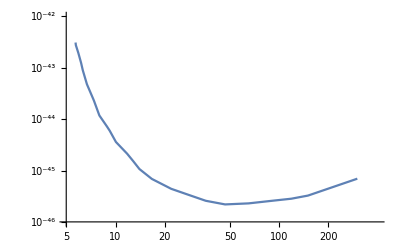

```mathematica
sp = {{72.,95.}, {108., 95.}, {143., 95.}, {179., 95.}, {200., 95.}, {226., 95.}, {262., 95.}}
sx = {{5.*10^0, 1./10^46}, {10.,1./10^46}, {20., 1./10^46}, {40, 1./10^46}, {60,1./10^46},{100., 1./10^46}, {200.,1./10^46}}
sq={{72., 95.}, {72., 126.}, {72., 142.}, {72., 164.}, {72., 179.}, {72., 194.}, {72., 224.}, {72., 242.}, {72., 263.}, {72., 277.}, 
{72., 293.}, {72., 323.}, {72., 340.}, {72., 361.}, {72., 377.}, {72., 392.}, {72., 437.}, {72., 462.}, {72., 475.}, {72., 490.}}
sy = {{5.*10^0, 1./10^46}, {5.*10^0, 2./10^46}, {5.*10^0, 3./10^46}, {5.*10^0, 5./10^46},{5.*10^0, 7./10^46}, {5.*10^0, 1./10^45}, {5.*10^0, 2./10^45}, {5.*10^0, 3./10^45},{5.*10^0, 5./10^45},
 {5.*10^0, 7./10^45}, {5.*10^0, 1./10^44}, {5.*10^0, 2./10^44},{5.*10^0, 3./10^44}, {5.*10^0, 5./10^44}, {5.*10^0, 7./10^44}, {5.*10^0, 1./10^43},{5.*10^0, 3./10^43},{5.*10^0, 5./10^43}, 
{5.*10^0,7./10^43}, {5.*10^0, 1./10^42}}

lpp = Fit[Table[{sx[[i,1]], sp[[i,1]]}, {i, 1, 7}], {1, Log[u]}, u]  (*fit of several x points*)
lap = lpp /. u -> 1 (*this is just to extract the B_x coefficient*)
lmp = lpp - lap /. u -> E  (*Extract the slope coefficient *)

lqq = Fit[Table[{sy[[i,2]], sq[[i,2]]}, {i, 1, 20}], {1, Log[u]}, u]  (*fit of several y points*)
laq = lqq /. u -> 1 (*extract the Subscript[B, y] coeff.*)
lmq = lqq - laq /. u -> E  (*Extract the Subscript[A, y] coeff.*)

qlux = Interpolation[{{77., 480.}, {78., 457.}, {79., 435.}, {82., 410.}, {84., 387.}, {87., 360.}, {92., 329.}, {96., 300.}, {103., 273.}, {108., 249.}, {117., 224.}, {125., 197.}, {134., 178.}, {148., 159.}, 
{161., 147.}, {173., 136.}, {187., 129.}, {204., 131.}, {221., 136.}, {235., 140.}, {247., 146.}, {258., 156.}}, InterpolationOrder -> 1]
σlux16[mΨ_] := E^((qlux[lap + lmp*Log[mΨ]] - laq)/lmq)  (* y=f(x(u))*)
pic2 = LogLogPlot[σlux16[m], {m, 5.7, 300}, PlotRange -> {{5, 400}, {1./10^46, 1/10^42}}]
```

LUX 2015

```mathematica
img=Import["lux_15.png"]
```

-Graphics-

```mathematica
xx = {{499.422,150.212},{563.545,150.212},{606.705,150.212},{668.362,151.445},{712.755,150.212},{747.283,150.212},{855.8,148.979},{917.457,150.212},{961.85,148.979},{995.145,150.212},{1023.51,150.212},{1048.17,151.445},{1067.9,148.979},{1086.4,150.212},{1102.43,150.212},{1209.71,150.212}}; 
  fun[u_, c_, r_] := Transpose[ReplacePart[Transpose[u], c -> r]]; x1 = fun[xx, 2, Table[150.212, {i, 1, Length[xx]}]]; Length[x1]
v1 = {{2., 10.^(-46)}, {3., 10.^(-46)}, {4., 10.^(-46)}, {6., 10.^(-46)}, {8., 10.^(-46)}, {10., 10.^(-46)}, {20., 10.^(-46)}, {30., 10.^(-46)}, {40, 10.^(-46)}, {50, 10.^(-46)}, 
    {60, 10.^(-46)}, {70, 10.^(-46)}, {80, 10.^(-46)}, {90, 10.^(-46)}, {100, 10.^(-46)}, {200, 10.^(-46)}}; Length[v1]
```

16

16

```mathematica
y1={{499.422,148.979},{501.888,241.464},{500.655,279.692},{501.888,369.711},{500.655,407.938},{501.888,500.424},{501.888,538.651},{499.422,629.904},{501.888,668.131},{500.655,758.15},{500.655,796.378}};
yy = fun[y1, 1, Table[499.422, {i, 1, Length[y1]}]]
Length[yy]
w1={{3.,10.^-46},{3.,5*10.^-46},{3.,10.^-45},{3.,5*10.^-45},{3.,10.^-44},{3.,5*10.^-44},{3.,10.^-43},{3.,5*10.^-43},{3.,10.^-42},{3.,5*10.^-42},{3.,10.^-41}};Length[w1]
```

{{499.422,148.979},{499.422,241.464},{499.422,279.692},{499.422,369.711},{499.422,407.938},{499.422,500.424},{499.422,538.651},{499.422,629.904},{499.422,668.131},{499.422,758.15},{499.422,796.378}}

11

11

```mathematica
xvf = Fit[Table[{v1[[i,1]], x1[[i,1]]}, {i, 1, 8}], {1, Log[u]}, u]
av = xvf /. u -> 1
mv = xvf - av /. u -> E
```

392.757+154.252 Log[u]

392.757

154.252

```mathematica
ywf = Fit[Table[{w1[[i,2]], yy[[i,2]]}, {i, 1, 11}], {1, Log[u]}, u]
au = ywf /. u -> 1
mu = ywf - au /. u -> E
```

6105.84+56.2301 Log[u]

6105.84

56.2301

```mathematica
g1=Interpolation[{{601.773,923.391},{605.472,876.532},{610.405,827.206},{625.202,756.917},{635.067,686.628},{648.632,631.137},{663.43,571.946},{679.461,511.522},{704.123,452.331},{731.252,393.141},{760.848,343.815},{786.744,309.287},{824.971,282.158},{860.732,261.195},{898.96,252.563},{932.254,247.63},{956.917,247.63},{980.347,252.563},{1008.71,253.796},{1035.84,259.961},{1067.9,268.593},{1101.19,280.925},{1143.12,293.256},{1177.65,303.121},{1210.94,311.753},{1244.24,327.784}}]
```

InterpolatingFunction[{{601.773,1244.24}},<>]

```mathematica
lux15[mΨ_] := E^((g1[av + mv*Log[mΨ]] - au)/mu)
```

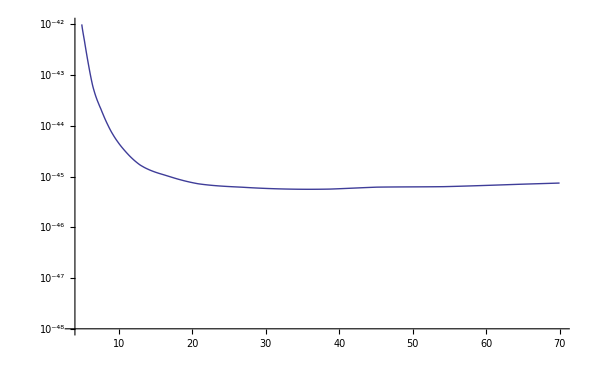

```mathematica
LogPlot[lux15[m],{m,4,70},PlotRange->{10^-48,10^-42}]
```

Xenon1T

```mathematica
img=Import["xenon1t.png"]
```

-Graphics-

```mathematica
vv= {{686.859, 274.759}, {721.387, 274.759}, {773.179, 274.759}, {816.339, 274.759}, {943.353, 274.759}, {1018.57, 274.759}, {1111.06, 277.225}, {1175.18, 273.526}, {1218.34, 275.992}, {1240.54, 275.992}, {1366.32, 275.992}, {1441.54, 275.992}};
vs=fun[vv,2,Table[ 296.956,{i,1,Length[vv]}]]
Length[vs]
xcs = {{5.,10.^(-47)}, {6.,10.^(-47)}, {8.,10.^(-47)}, {10.,10.^(-47)}, {20.,10.^(-47)},{30,10.^(-47)},{50,10.^(-47)},{70,10.^(-47)},{90,10.^(-47)},{100,10.^(-47)},{200,10.^(-47)},{300,10.^(-47)}};Length[xcs]
us = {{686.859, 296.956}, {686.859, 374.644}, {686.859, 452.331}, {686.859, 528.786}, {686.859, 607.707}, {686.859, 682.929},{686.859, 761.85}};

ycs = {{5., 10.^(-47)}, {5., 10.^(-46)},{5., 10.^(-45)}, {5., 10.^(-44)},{5., 10.^(-43)},{5.,10.^(-42)},{5.,10.^(-41)}}
```

{{686.859,296.956},{721.387,296.956},{773.179,296.956},{816.339,296.956},{943.353,296.956},{1018.57,296.956},{1111.06,296.956},{1175.18,296.956},{1218.34,296.956},{1240.54,296.956},{1366.32,296.956},{1441.54,296.956}}

12

12

{{5.,1.×10^-47},{5.,1.×10^-46},{5.,1.×10^-45},{5.,1.×10^-44},{5.,1.×10^-43},{5.,1.×10^-42},{5.,1.×10^-41}}

```mathematica
vf = Fit[Table[{xcs[[i,1]], vs[[i,1]]}, {i, 1, 12}], {1, Log[u]}, u]
avs = vf /. u -> 1
mvs = vf - avs /. u -> E
```

391.252+184.171 Log[u]

391.252

184.171

```mathematica
uf = Fit[Table[{ycs[[i,2]], us[[i,2]]}, {i, 1, 6}], {1, Log[u]}, u]
aus = uf /. u -> 1
mus = uf - aus /. u -> E
```

3930.42+33.5711 Log[u]

3930.42

33.5711

```mathematica
FT = Interpolation[{{727.553, 719.923}, {743.584, 665.665}, {770.713, 605.241}, {800.308, 537.418}, {831.137, 483.16}, {865.665, 431.368}, {916.224, 382.042}, {964.316, 349.981}, {1008.71, 332.717}, {1050.64, 324.085}, {1092.56, 317.919}, {1143.12, 316.686}, {1193.68, 319.152}, {1244.24, 324.085}, {1298.5, 332.717}, {1357.69, 337.649}, {1399.61, 345.048}}, InterpolationOrder -> 1]
```

InterpolatingFunction[{{727.553,1399.61}},<>]

```mathematica
xenon1t[mΨ_] := E^((FT[avs + mvs*Log[mΨ]] - aus)/mus)
```

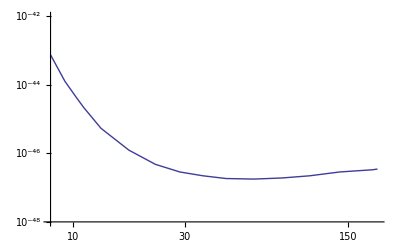

```mathematica
LogLogPlot[xenon1t[m],{m,8,200},PlotRange->{10^-48,10^-42}]
```

```mathematica
data = Cases[Plot[σlux[m], {m, 4,70}], Line[data_] :> data, -4, 1][[1]];
```

```mathematica
Export["lux.dat",data]
```

```mathematica
data2 = Cases[Plot[xenon1t[m], {m, 4,70}], Line[data_] :> data, -4, 1][[1]];
```

```mathematica
Export["xenon1t.dat",data2]
```

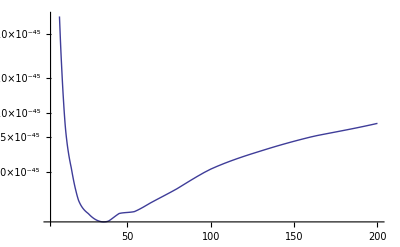

```mathematica
LogPlot[lux15[m], {m, 4,200}]
```

```mathematica
data3 = Cases[LogPlot[lux15[m], {m, 4,100}], Line[data_] :> data, -4, 1][[1]];
```

```mathematica
Export["Lux15_log.dat",data3]
```

Lux15_log.dat

```mathematica
Export["lux15_2.txt",Cases[Plot[lux15[m],{m,4,70},PlotRange->{10^-46,10^-42}],Line@data__->data,Infinity],"Table"]
```

lux15_2.txt

```mathematica
ParentDirectory[]
```

/home/vanniagm/Dropbox/nu_portal